```mathematica
Quit[]
```

## Declarations

```mathematica
<<FractionalIteration`
```

```mathematica
A[x,y,3]
```

x ↑^3 y

```mathematica
SuperPower[x,a]
SuperExp[a,x]
```

x ↑^2 a

a ↑^2 x

```mathematica
??FractionalIteration`*
```

```mathematica
A[x,3][y]
```

x ↑^3 y

```mathematica
p[n_Integer/;n>1]:=A[x,-∞,n]
```

```mathematica
p[0]
```

p[0]

```mathematica
A[x_,y,2]:=A[x,∞,1]
```

```mathematica
Ackermann[a,b,n]
```

Ackermann[a,b,n]

```mathematica
A[a,1][A[a,1,2][z]]
```

a^((a ↑^2)[z])

```mathematica
A[a,1][z]
```

A[a,1][z]

```mathematica
A[a_,b_,n_]:=Ackermann[a,b,n]
```

```mathematica
A[a_,n_][b_]:=Ackermann[a,b,n]
```

```mathematica
Format[Ackermann[a_,b_,n_]]:= HoldForm[a Superscript["↑",n]b];
```

```mathematica
Format[Ackermann[a_,n_][b_]]:= HoldForm[a Superscript["↑",n]b];

A[a,b,n]
```

a ↑^n b

```mathematica
A[a,n][b]
```

a ↑^n b

```mathematica
p[2]=A[a,2][A[a,1][z]]
```

a ↑^2 (a ↑^1 z)

```mathematica
A[a,1][∞]
```

Infinity::indet: Indeterminate expression a^∞ encountered.

Indeterminate

## Quit

```mathematica
Quit[]
```

## Work

```mathematica
<<FractionalIteration`
```

```mathematica
ToCharacterCode["o"]
```

{111}

```mathematica
FractionalIteration[f,n,x,p,2]
```

{True,Universal,Symbolic}

p+(-p+x) f'[p]^n+1/2 (-p+x)^2 (∑_(k_1=0)^(-1+n) f'[p]^(-2+2 n-k_1)) f''[p]

```mathematica
FractionalIteration[f,n,x,p,
```

```mathematica
b=Exp[1];
branch=0;
(*f[z_]:=N[Log[b,z]+2 Pi I branch]*)
f[z_]:=N[Log[z]]
p=FixedPoint[f,1.0+I]
```

0.318132+1.33724 ⅈ

```mathematica
??f
```

```mathematica
p=FixedPoint[Log,1.0+I]
```

0.318132+1.33724 ⅈ

```mathematica
FractionalIteration[f,n,z,FixedPoint[Log,1.0+I],2] /.HoldForm->Identity /.z->1
```

{True,Universal,Symbolic}

(0.318132+1.33724 ⅈ)+(0.681868-1.33724 ⅈ) (0.168376-0.707754 ⅈ)^n+(7.23683×10^-35-1.63651×10^-32 ⅈ) (1.56735×10^15-6.58819×10^15 ⅈ)^n (9.30859×10^15)^(2.-1. n) (-1.+(0.168376-0.707754 ⅈ)^n)

```mathematica
p+(-p+z) f'[p]^n+((-p+z)^2 f'[p]^(-1+n) (-1+f'[p]^n) f''[p])/(2 (-1+f'[p])) /.z->1
```

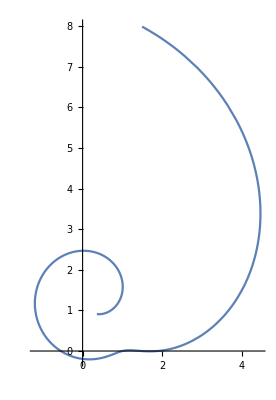

```mathematica
ParametricPlot[{Re[(0.318131505204764+1.3372357014306895 ⅈ)+(0.681868494795236-1.3372357014306895 ⅈ) (0.16837637908722283-0.7077541887847276 ⅈ)^n+(0.4158118104563885+0.3538770943923638 ⅈ) (0.16837637908722283-0.7077541887847276 ⅈ)^(-1+n) (-1+(0.16837637908722283-0.7077541887847276 ⅈ)^n)],Im[(0.318131505204764+1.3372357014306895 ⅈ)+(0.681868494795236-1.3372357014306895 ⅈ) (0.16837637908722283-0.7077541887847276 ⅈ)^n+(0.4158118104563885+0.3538770943923638 ⅈ) (0.16837637908722283-0.7077541887847276 ⅈ)^(-1+n) (-1+(0.16837637908722283-0.7077541887847276 ⅈ)^n)]},{n,-2,5}]
```

```mathematica
AbsArgPlot[(0.318131505204764+1.3372357014306895 ⅈ)+(0.681868494795236-1.3372357014306895 ⅈ) (0.16837637908722283-0.7077541887847276 ⅈ)^n+(0.4158118104563885+0.3538770943923638 ⅈ) (0.16837637908722283-0.7077541887847276 ⅈ)^(-1+n) (-1+(0.16837637908722283-0.7077541887847276 ⅈ)^n),{n,-10,10}]
```

-Graphics-

```mathematica
??Globel`*
```

Missing[UnknownSymbol,Globel`*]

```mathematica
??A
```

Missing[UnknownSymbol,A]